```mathematica
k=.175;
c=100;
dt=0.1;
T=Range[0,1,dt];
cc = {c};

For[ i=1,i<Length[T],
   c=c+-k*dt*c;
AppendTo[cc,c];
i++;
]
```

```mathematica
data=Transpose@{T, cc};
```

11

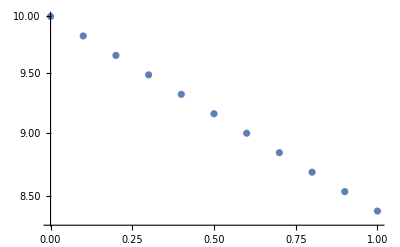

```mathematica
ListLogPlot[data]
```